# AntonAntonov/NumberTheoryUtilities

Number Theory utility functions

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"ChordTrailsPlot.nb"DocumentationEnglishReferencePagesSymbolsChordTrailsPlot.nb

"SpiralLattice.nb"DocumentationEnglishReferencePagesSymbolsSpiralLattice.nb

"SunflowerEmbedding.nb"DocumentationEnglishReferencePagesSymbolsSunflowerEmbedding.nb

"SunflowerEmbeddingPlot.nb"DocumentationEnglishReferencePagesSymbolsSunflowerEmbeddingPlot.nb

"TriangleMatrixEmbedding.nb"DocumentationEnglishReferencePagesSymbolsTriangleMatrixEmbedding.nb

"Tutorials"

"Kernel"

"NumberTheoryUtilities.wl"KernelNumberTheoryUtilities.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

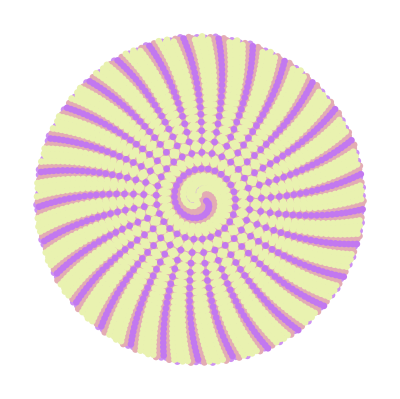

### Basic Description

Utility functions for visualizing Number theory relationships and phenomena.

### Details

The functions TriangularEmbedding and SpiralEmbedding give data structures for making Klauber triangles and Ulam spirals.

The function SunbflowerEmbedding and SunbflowerEmbeddingPlot are used to make sunflower embeddings data visualizations.

SunbflowerEmbedding can be given a function that classifies the numbers into groups.

SunbflowerEmbeddingPlot uses those groups to color the corresponding points.

ChordTrailsPlot and SunbflowerEmbeddingPlot uses all options of Graphics.

### Primary Context

AntonAntonov`NumberTheoryUtilities`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`NumberTheoryUtilities`"];
```

### Basic Examples

Make a Ulam's spiral embedding of integers within a square with 16 rows and columns:

```mathematica
SpiralLattice[16]//Grid
```

226 | 225 | 224 | 223 | 222 | 221 | 220 | 219 | 218 | 217 | 216 | 215 | 214 | 213 | 212 | 211
227 | 170 | 169 | 168 | 167 | 166 | 165 | 164 | 163 | 162 | 161 | 160 | 159 | 158 | 157 | 210
228 | 171 | 122 | 121 | 120 | 119 | 118 | 117 | 116 | 115 | 114 | 113 | 112 | 111 | 156 | 209
229 | 172 | 123 | 82 | 81 | 80 | 79 | 78 | 77 | 76 | 75 | 74 | 73 | 110 | 155 | 208
230 | 173 | 124 | 83 | 50 | 49 | 48 | 47 | 46 | 45 | 44 | 43 | 72 | 109 | 154 | 207
231 | 174 | 125 | 84 | 51 | 26 | 25 | 24 | 23 | 22 | 21 | 42 | 71 | 108 | 153 | 206
232 | 175 | 126 | 85 | 52 | 27 | 10 | 9 | 8 | 7 | 20 | 41 | 70 | 107 | 152 | 205
233 | 176 | 127 | 86 | 53 | 28 | 11 | 2 | 1 | 6 | 19 | 40 | 69 | 106 | 151 | 204
234 | 177 | 128 | 87 | 54 | 29 | 12 | 3 | 4 | 5 | 18 | 39 | 68 | 105 | 150 | 203
235 | 178 | 129 | 88 | 55 | 30 | 13 | 14 | 15 | 16 | 17 | 38 | 67 | 104 | 149 | 202
236 | 179 | 130 | 89 | 56 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 66 | 103 | 148 | 201
237 | 180 | 131 | 90 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 102 | 147 | 200
238 | 181 | 132 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 146 | 199
239 | 182 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 198
240 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197
241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256

Make a triangular embedding of integers up to 12 triangle rows:

```mathematica
TriangleMatrixEmbedding[10, ""]//Grid
```

|  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 2 | 3 | 4 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 5 | 6 | 7 | 8 | 9 |  |  |  |  |  |  | 
 |  |  |  |  |  | 10 | 11 | 12 | 13 | 14 | 15 | 16 |  |  |  |  |  | 
 |  |  |  |  | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 |  |  |  |  | 
 |  |  |  | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 |  |  |  | 
 |  |  | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 |  |  | 
 |  | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 |  | 
 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 
82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

Sunflower embedding of integers up to 2000 with primes shown in red:

```mathematica
SunflowerEmbeddingPlot[2000,Boole@*PrimeQ,PlotStyle->{PointSize[0.016]},ColorFunction->(Blend[{GrayLevel[0.8],Red},#]&)]//Image
```

-Graphics-

### Scope

Show Klauber triangle:

```mathematica
Grid[TriangleMatrixEmbedding[17, ""]/.{(x_?PrimeQ):>Style[x,Red,Bold]}]
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 2 | 3 | 4 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 5 | 6 | 7 | 8 | 9 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 10 | 11 | 12 | 13 | 14 | 15 | 16 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 |  |  |  |  |  |  | 
 |  |  |  |  |  | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 |  |  |  |  |  | 
 |  |  |  |  | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 |  |  |  |  | 
 |  |  |  | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 |  |  |  | 
 |  |  | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 |  |  | 
 |  | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 |  | 
 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 
257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289

Show Ulam's spiral (finishing top-right):

```mathematica
s=SpiralLattice[27,"top-right"];
s2=s/.{(x_Integer/;!PrimeQ[x]):>""}/.{(x_Integer):>Style[x,Red]};
Grid[s2]
```

|  |  |  |  |  | 709 |  |  |  |  |  |  |  |  |  | 719 |  |  |  |  |  |  |  | 727 |  | 
 | 601 |  |  |  |  |  | 607 |  |  |  |  |  | 613 |  |  |  | 617 |  | 619 |  |  |  |  |  |  | 
701 |  |  |  | 509 |  |  |  |  |  |  |  |  |  |  |  | 521 |  | 523 |  |  |  |  |  |  |  | 
 | 599 |  | 421 |  |  |  |  |  |  |  |  |  | 431 |  | 433 |  |  |  |  |  | 439 |  |  |  |  | 
 |  |  |  |  |  |  |  | 347 |  | 349 |  |  |  | 353 |  |  |  |  |  | 359 |  |  |  | 443 |  | 
 |  |  | 419 |  |  |  |  |  | 277 |  |  |  | 281 |  | 283 |  |  |  |  |  |  |  |  |  |  | 
 |  | 503 |  |  |  | 211 |  |  |  |  |  |  |  |  |  |  |  | 223 |  |  |  |  |  |  |  | 631
 |  |  |  |  | 271 |  | 157 |  |  |  |  |  | 163 |  |  |  | 167 |  |  |  | 227 |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  | 113 |  |  |  |  |  |  |  |  |  |  |  | 293 |  |  |  | 
 | 593 |  |  |  | 269 |  |  |  | 73 |  |  |  |  |  | 79 |  |  |  |  |  | 229 |  | 367 |  |  | 
 |  | 499 |  | 337 |  |  |  | 109 |  | 43 |  |  |  | 47 |  |  |  | 83 |  | 173 |  |  |  | 449 |  | 
 |  |  |  |  |  |  |  |  | 71 |  |  |  | 23 |  |  |  |  |  |  |  |  |  |  |  |  | 
691 |  |  |  |  |  |  |  | 107 |  | 41 |  | 7 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 151 |  |  |  | 19 |  |  | 2 | 11 |  | 53 |  | 127 |  | 233 |  |  |  | 541 | 
 |  |  |  |  |  |  |  |  |  |  |  | 5 |  | 3 |  | 29 |  |  |  |  |  |  |  |  |  | 
 | 587 |  | 409 |  | 263 |  | 149 |  | 67 |  | 17 |  |  |  | 13 |  |  |  |  |  |  |  | 373 |  |  | 
 |  |  |  | 331 |  |  |  | 103 |  | 37 |  |  |  |  |  | 31 |  | 89 |  | 179 |  |  |  |  |  | 641
 |  |  |  |  |  |  |  |  |  |  |  |  | 61 |  | 59 |  |  |  | 131 |  |  |  |  |  |  | 
 |  | 491 |  |  |  | 199 |  | 101 |  |  |  | 97 |  |  |  |  |  |  |  | 181 |  |  |  | 457 |  | 643
 |  |  |  |  |  |  |  |  |  |  |  |  | 139 |  | 137 |  |  |  |  |  | 239 |  |  |  | 547 | 
683 |  |  |  |  |  | 197 |  |  |  | 193 |  | 191 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  | 257 |  |  |  |  |  | 251 |  |  |  |  |  |  |  |  |  | 241 |  | 379 |  |  | 
 |  | 487 |  |  |  |  |  |  |  |  |  | 317 |  |  |  | 313 |  | 311 |  |  |  | 307 |  | 461 |  | 647
 |  |  | 401 |  |  |  | 397 |  |  |  |  |  |  |  | 389 |  |  |  |  |  | 383 |  |  |  |  | 
 |  |  |  |  |  |  |  | 479 |  |  |  |  |  |  |  |  |  |  |  | 467 |  |  |  | 463 |  | 
 | 577 |  |  |  |  |  | 571 |  | 569 |  |  |  |  |  | 563 |  |  |  |  |  | 557 |  |  |  |  | 
677 |  |  |  | 673 |  |  |  |  |  |  |  |  |  |  |  | 661 |  | 659 |  |  |  |  |  | 653 |  |

Show primitive root chord trails plot of 509 for its primitive root 75:

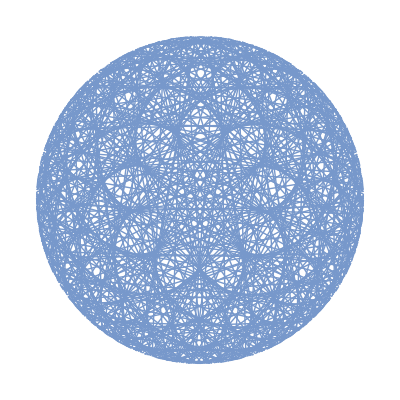

```mathematica
ChordTrailsPlot[509,75]
```

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-NumberTheoryUtilities-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Number theory

Ulam spiral

Triangular embedding

Spiral embedding

Sunflower embedding

Chords plot

Chord trails plot

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

UlamMatrix

SquareSpiralPoints

LatticePointsArrangement

### Original Source References and Attributions

GitHub - antononcube/Raku-Math-NumberTheory: Raku package with number theory functions.

### Links

Anton Antonov, "Primitive roots generation trails", (2025), Wolfram Community.

Number theory neat examples in Raku (Set 1) - YouTube

Number theory neat examples in Raku (Set 2) - YouTube

Number theory neat examples in Raku (Set 3) - YouTube

### Compatibility

#### Wolfram Language Version

14.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.